```mathematica
psi[x_,ξ_,n_]:=ξ^(1/4)/π^(1/4)*Exp[(-ξ*x^2)/2]*HermiteH[n,x*Sqrt[ξ]]/Sqrt[2^n*Gamma[n+1]]
```

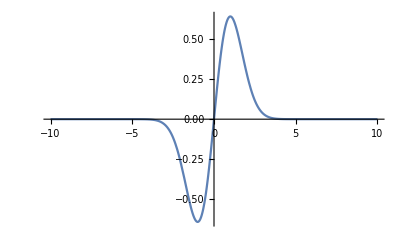

```mathematica
Plot[psi[x,1,1],{x,-10,10},PlotRange->All]
```

```mathematica
tf=1
```

1

```mathematica
ξ1=1/7
```

1/7

```mathematica
ξ2=1/3
```

1/3

```mathematica
n1=0
```

0

```mathematica
n2=0
```

0

```mathematica
η[t_,tf_]:=(t/tf)^3(1+3(1-(t/tf))+6*(1-(t/tf))^2)
```

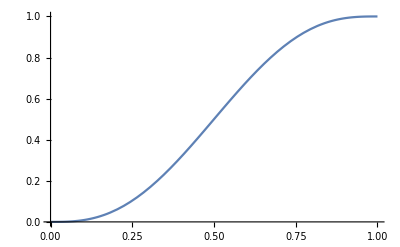

```mathematica
Plot[η[t,tf],{t,0,tf}, PlotRange->All]
```

```mathematica
ϕ[t_,tf_]:=(t/tf)(1-(t/tf))(0.5*(ξ1+ξ2)t-0.5*ξ1*tf)
```

```mathematica
ρ[x_,t_,ξ1_,n1_, ξ2_,n2_,tf_]:=psi[x,ξ1,n1]*((1-η[t,tf]))+psi[x,ξ2,n2]*(η[t,tf])
```

```mathematica
ρ[x,t,ξ1,n1, ξ2,n2,tf]
```

(ⅇ^(-x^2/6) (1+3 (1-t)+6 (1-t)^2) t^3)/(3 π)^(1/4)+(ⅇ^(-x^2/14) (1-(1+3 (1-t)+6 (1-t)^2) t^3))/(7 π)^(1/4)

```mathematica
Plot3D[ρ[x,t,ξ1,n1, ξ2,n2,tf],{x,-10,10},{t,0,tf},PlotRange->All]
```

-Graphics3D-

```mathematica
Norma[t_,ξ1_,n1_, ξ2_,n2_,tf_]:=Integrate[ρ[x,t,ξ1,n1, ξ2,n2,tf]^2,{x,-∞,∞},Assumptions->Element[n1,Integers]&&Element[n2,Integers]&& Element[ξ1,Reals]&& Element[ξ2,Reals]]
```

```mathematica
ρn[x_,t_,ξ1_,n1_, ξ2_,n2_,tf_]:=ρ[x,t,ξ1,n1, ξ2,n2,tf]/Sqrt[Norma[t,ξ1,n1, ξ2,n2,tf]]
```

```mathematica
ρn[x,t,ξ1,n1, ξ2,n2,tf]
```

(√5 ((ⅇ^(-x^2/6) (1+3 (1-t)+6 (1-t)^2) t^3)/(3 π)^(1/4)+(ⅇ^(-x^2/14) (1-(1+3 (1-t)+6 (1-t)^2) t^3))/(7 π)^(1/4)))/(√(5-2 (-5+√5 21^(1/4)) (-1+t)^3 t^3 (1+3 t+6 t^2) (10+3 t (-5+2 t))))

```mathematica
ρnn[x_,t_]=ρn[x,t,ξ1,n1, ξ2,n2,tf]
```

(√5 ((ⅇ^(-x^2/6) (1+3 (1-t)+6 (1-t)^2) t^3)/(3 π)^(1/4)+(ⅇ^(-x^2/14) (1-(1+3 (1-t)+6 (1-t)^2) t^3))/(7 π)^(1/4)))/(√(5-2 (-5+√5 21^(1/4)) (-1+t)^3 t^3 (1+3 t+6 t^2) (10+3 t (-5+2 t))))

```mathematica
ρnnt[x_,t_,a_,b_]=((a^(1/4) ⅇ^(-(a x^2)/2) (1+3 (1-t)+6 (1-t)^2) t^3)/π^(1/4)+(b^(1/4) ⅇ^(-(b x^2)/2) (1-(1+3 (1-t)+6 (1-t)^2) t^3))/π^(1/4))/(√((√(a+b)-2 (√2 (a b)^(1/4)-√(a+b)) (-1+t)^3 t^3 (1+3 t+6 t^2) (10+3 t (-5+2 t)))/(√(a+b))))
```

((a^(1/4) ⅇ^(-(a x^2)/2) (1+3 (1-t)+6 (1-t)^2) t^3)/π^(1/4)+(b^(1/4) ⅇ^(-(b x^2)/2) (1-(1+3 (1-t)+6 (1-t)^2) t^3))/π^(1/4))/(√((√(a+b)-2 (√2 (a b)^(1/4)-√(a+b)) (-1+t)^3 t^3 (1+3 t+6 t^2) (10+3 t (-5+2 t)))/(√(a+b))))

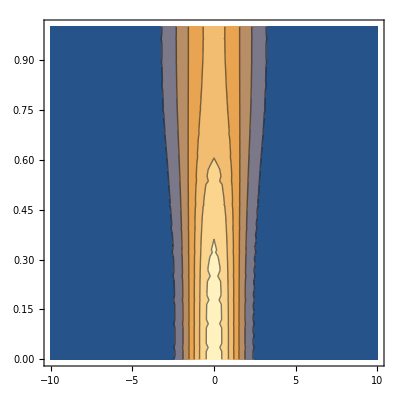

```mathematica
ContourPlot[ρnnt[x,t,ξ1,ξ2]^2,{x,-10,10},{t,0,tf},PlotRange->All]
```

```mathematica
dtρnn2[x_,t_,a_,b_]:=D[ρnnt[x,t,a,b]^2,t]
```

```mathematica
intdtρnn2[x_,t_,a_,b_]:=Integrate[dtρnn2[u,t,a,b],{u,0,x}]
```

```mathematica
U[x_,t_,a_,b_]=Simplify[intdtρnn2[x,t,a,b]/ρnn[x,t,a,b]^2]
```

(30 √(a+b) (-1+t)^2 t^2 x (-√a t^3 (10-15 t+6 t^2) (-√(a+b)-10 (√2 (a b)^(1/4)-√(a+b)) t^3+15 (√2 (a b)^(1/4)-√(a+b)) t^4+(-6 √2 (a b)^(1/4)+6 √(a+b)) t^5) √(b x^2) √((a+b) x^2) Erf[√(a x^2)]+b^(1/4) √(a x^2) (-b^(1/4) (-1+t)^3 (1+3 t+6 t^2) (-√2 (a b)^(1/4)+10 (√2 (a b)^(1/4)-√(a+b)) t^3-15 (√2 (a b)^(1/4)-√(a+b)) t^4+6 (√2 (a b)^(1/4)-√(a+b)) t^5) √((a+b) x^2) Erf[√(b x^2)]+√2 a^(1/4) √(a+b) (1-20 t^3+30 t^4-12 t^5) √(b x^2) Erf[(√((a+b) x^2))/(√2)])))/((√(a+b)+20 (√2 (a b)^(1/4)-√(a+b)) t^3-30 (√2 (a b)^(1/4)-√(a+b)) t^4+12 (√2 (a b)^(1/4)-√(a+b)) t^5-200 (√2 (a b)^(1/4)-√(a+b)) t^6+600 (√2 (a b)^(1/4)-√(a+b)) t^7-690 (√2 (a b)^(1/4)-√(a+b)) t^8+360 (√2 (a b)^(1/4)-√(a+b)) t^9-72 (√2 (a b)^(1/4)-√(a+b)) t^10)^2 √(a x^2) √(b x^2) √((a+b) x^2) ρnn[x,t,a,b]^2)

```mathematica
U2[x_,t_,a_,b_]:=(30 √(a+b) (-1+t)^2 t^2 x (-√a t^3 (10-15 t+6 t^2) (-√(a+b)-10 (√2 (a b)^(1/4)-√(a+b)) t^3+15 (√2 (a b)^(1/4)-√(a+b)) t^4+(-6 √2 (a b)^(1/4)+6 √(a+b)) t^5) √(b x^2) √((a+b) x^2) Erf[√(a x^2)]+b^(1/4) √(a x^2) (-b^(1/4) (-1+t)^3 (1+3 t+6 t^2) (-√2 (a b)^(1/4)+10 (√2 (a b)^(1/4)-√(a+b)) t^3-15 (√2 (a b)^(1/4)-√(a+b)) t^4+6 (√2 (a b)^(1/4)-√(a+b)) t^5) √((a+b) x^2) Erf[√(b x^2)]+√2 a^(1/4) √(a+b) (1-20 t^3+30 t^4-12 t^5) √(b x^2) Erf[(√((a+b) x^2))/(√2)])))/((√(a+b)+20 (√2 (a b)^(1/4)-√(a+b)) t^3-30 (√2 (a b)^(1/4)-√(a+b)) t^4+12 (√2 (a b)^(1/4)-√(a+b)) t^5-200 (√2 (a b)^(1/4)-√(a+b)) t^6+600 (√2 (a b)^(1/4)-√(a+b)) t^7-690 (√2 (a b)^(1/4)-√(a+b)) t^8+360 (√2 (a b)^(1/4)-√(a+b)) t^9-72 (√2 (a b)^(1/4)-√(a+b)) t^10)^2 √(a x^2) √(b x^2) √((a+b) x^2) *((√5 ((ⅇ^(-x^2/6) (1+3 (1-t)+6 (1-t)^2) t^3)/(3 π)^(1/4)+(ⅇ^(-x^2/14) (1-(1+3 (1-t)+6 (1-t)^2) t^3))/(7 π)^(1/4)))/(√(5-2 (-5+√5 21^(1/4)) (-1+t)^3 t^3 (1+3 t+6 t^2) (10+3 t (-5+2 t)))))^2)
```

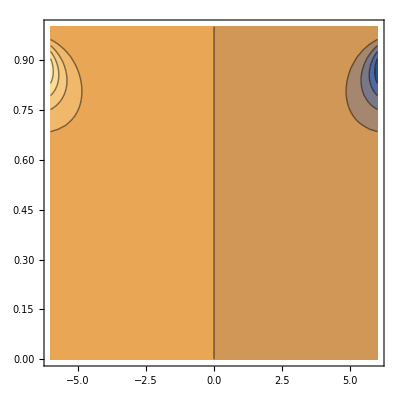

```mathematica
ContourPlot[U2[x,t,ξ1,ξ2],{x,-6,6},{t,0,tf},PlotRange->All]
```

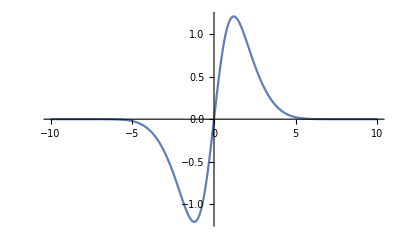

```mathematica
Plot[U2[x,0.5,1, 1/3],{x,-10,10},PlotRange->All]
```

```mathematica
fourth[t_]= -D[ϕ[t,tf],t]
```

-(1-t) (-0.0714286+0.238095 t)-0.238095 (1-t) t+(-0.0714286+0.238095 t) t

```mathematica
third[x_,t_]=-0.5*U2[x,t,ξ1,ξ2]^2
```

-((378. (-1+t)^4 t^4 (5-2 (-5+√5 21^(1/4)) (-1+t)^3 t^3 (1+3 t+6 t^2) (10+3 t (-5+2 t)))^2 (1/(3^(1/4) √7)√(x^2) ((2 √5 (1-20 t^3+30 t^4-12 t^5) √(x^2) Erf[√(5/21) √(x^2)])/(3 7^(3/4))-1/3^(3/4)√(10/7) (-1+t)^3 (1+3 t+6 t^2) (-(√2)/21^(1/4)+10 (-√(10/21)+(√2)/21^(1/4)) t^3-15 (-√(10/21)+(√2)/21^(1/4)) t^4+6 (-√(10/21)+(√2)/21^(1/4)) t^5) √(x^2) Erf[(√(x^2))/(√3)])-1/21 √10 t^3 (10-15 t+6 t^2) (-√(10/21)-10 (-√(10/21)+(√2)/21^(1/4)) t^3+15 (-√(10/21)+(√2)/21^(1/4)) t^4+(2 √(30/7)-(2 √2 3^(3/4))/7^(1/4)) t^5) x^2 Erf[(√(x^2))/(√7)])^2)/((√(10/21)+20 (-√(10/21)+(√2)/21^(1/4)) t^3-30 (-√(10/21)+(√2)/21^(1/4)) t^4+12 (-√(10/21)+(√2)/21^(1/4)) t^5-200 (-√(10/21)+(√2)/21^(1/4)) t^6+600 (-√(10/21)+(√2)/21^(1/4)) t^7-690 (-√(10/21)+(√2)/21^(1/4)) t^8+360 (-√(10/21)+(√2)/21^(1/4)) t^9-72 (-√(10/21)+(√2)/21^(1/4)) t^10)^4 ((ⅇ^(-x^2/6) (1+3 (1-t)+6 (1-t)^2) t^3)/(3 π)^(1/4)+(ⅇ^(-x^2/14) (1-(1+3 (1-t)+6 (1-t)^2) t^3))/(7 π)^(1/4))^4 x^4))

```mathematica
second[x_,t_]=D[D[ρnn[x,t],x],x]/ρnn[x,t]
```

(-(ⅇ^(-x^2/6) (1+3 (1-t)+6 (1-t)^2) t^3)/(3 (3 π)^(1/4))-(ⅇ^(-x^2/14) (1-(1+3 (1-t)+6 (1-t)^2) t^3))/(7 (7 π)^(1/4))+(ⅇ^(-x^2/6) (1+3 (1-t)+6 (1-t)^2) t^3 x^2)/(9 (3 π)^(1/4))+(ⅇ^(-x^2/14) (1-(1+3 (1-t)+6 (1-t)^2) t^3) x^2)/(49 (7 π)^(1/4)))/((ⅇ^(-x^2/6) (1+3 (1-t)+6 (1-t)^2) t^3)/(3 π)^(1/4)+(ⅇ^(-x^2/14) (1-(1+3 (1-t)+6 (1-t)^2) t^3))/(7 π)^(1/4))

```mathematica
preh[x_,t_]:=second[x,t]+third[x,t]+fourth[t]
```

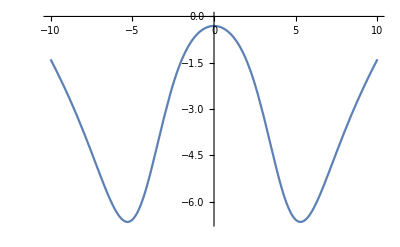

```mathematica
Plot[preh[x,0.5],{x,-10,10}]
```

```mathematica
prefirst[x_,t_]=D[U2[x,t,ξ1,ξ2],t];
```

```mathematica
Plot3D[prefirst[x,t],{x,-9,9},{t,0.007,tf}, PlotRange->All]
```

-Graphics3D-

```mathematica
first[x_,t]:=NIntegrate[prefirst[h,t],{h,0,x},PrecisionGoal->10]
```

```mathematica
Plot3D[first[x,t],{x,-9,9},{t,0.0,tf}, PlotRange->All]
```

-Graphics3D-

```mathematica
full[x_,t_]:=second[x,t]+third[x,t]+fourth[t]+first[x,t]
```

```mathematica
Plot3D[full[x,t],{x,-5,5},{t,0.0,tf}, PlotRange->All]
```

-Graphics3D-

```mathematica
VT=Table[full[x,t],{x,-10,10,0.2},{t,0.0,tf,0.01}];
```

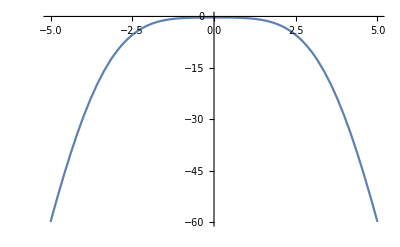

```mathematica
Plot[full[x,0.5],{x,-5,5}]
```

```mathematica
ListPlot3D[VT]
```

-Graphics3D-

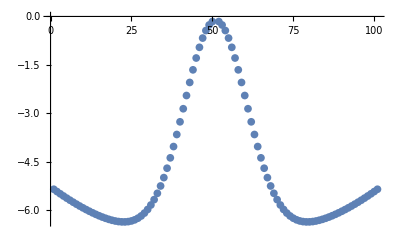

```mathematica
ListPlot[VT[[All,10]],PlotRange->All]
```

```mathematica
Export["VT.dat",VT]
```

VT.dat

```mathematica
SystemOpen["VT.dat"]
```